```mathematica
Clear["Global`*"]
```

```mathematica
M=1
V0=8*10^{-11}*M^4
```

1

{1/12500000000}

```mathematica
V=V0(1-Exp[-√(2/3) f/M])^2
```

{((1-ⅇ^(-√(2/3) f))^2)/12500000000}

```mathematica
dV=D[V,f]
```

{(ⅇ^(-√(2/3) f) (1-ⅇ^(-√(2/3) f)))/(3125000000 √6)}

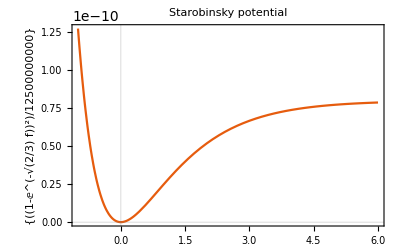

```mathematica
Plot[V,{f,-1 M,6 M},AxesLabel->StandardForm[V],PlotTheme->"Scientific",PlotLabel->"Starobinsky potential"]
```

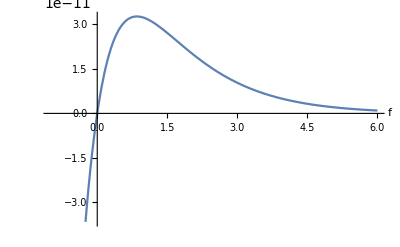

```mathematica
Plot[dV,{f,-1 M,6M},AxesLabel->Automatic]
```

```mathematica
ddV=D[dV,f]
Condition1=Abs[dV]/V^{3/2}
Bound1= Sqrt[2]/(2π M^3)
```

{ⅇ^(-2 √(2/3) f)/9375000000-(ⅇ^(-√(2/3) f) (1-ⅇ^(-√(2/3) f)))/9375000000}

{(100000 √(10/3) ⅇ^(-√(2/3) Re[f]) Abs[1-ⅇ^(-√(2/3) f)])/(((1-ⅇ^(-√(2/3) f))^2)^(3/2))}

1/(√2 π)

```mathematica
Plot[{(100000 √(10/3) ⅇ^(-√(2/3) Re[f]) Abs[1-ⅇ^(-√(2/3) f)])/(((1-ⅇ^(-√(2/3) f))^2)^(3/2)),Bound1},{f,10,25},PlotRange->{0,2},PlotLabels->{"|V'|/V^{3/2}","bound"},PlotLabel->"Condition 1",Filling->{2->Axis},ImageSize->Large]
```

-Graphics-

```mathematica
FindRoot[Condition1==Bound1,{f,10}]
```

{f→16.6641}